#### Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dX[n_]:=Symbol["d"<>ToString[coord[[n]]]]
```

```mathematica
$Assumptions=And[u∈Reals,r∈Reals,v∈Reals,r>Tu+Tv>0,Tu>0,Tv>0,L>0,T>0,r>2T,x∈Reals];
```

```mathematica
coord={u,v,r};
metricSign=-1;
```

#### Poincaré to BTZ

```mathematica
u2btz=u->√((r^2-(Tu+Tv)^2)/(r^2-(Tu-Tv)^2))E^(2u*Tu);
v2btz=(u2btz/.u->v/.{Tu->Tv,Tv->Tu})//Simplify
z2btz=z->√(((Tu+Tv)^2-(Tu-Tv)^2)/(r^2-(Tu-Tv)^2))Exp[(u+v)/2(Tu+Tv)+(u-v)/2(Tu-Tv)]//Simplify
poincare2btz={u2btz,v2btz,z2btz};
```

v→ⅇ^(2 Tv v) √((r^2-(Tu+Tv)^2)/(r^2-(Tu-Tv)^2))

z→2 ⅇ^(Tu u+Tv v) √((Tu Tv)/(r^2-(Tu-Tv)^2))

```mathematica
(Dt[u]Dt[v]+Dt[z]^2)/z^2/.poincare2btz/.(Dt[#]->0&/@{Tu,Tv})//Simplify

(r^2-(Tu+Tv)^2)(r^2-(Tu-Tv)^2)==r^4+(Tu^2-Tv^2)^2-2 r^2 (Tu^2+Tv^2)//Simplify
```

(r^2 Dt[r]^2)/(r^4+(Tu^2-Tv^2)^2-2 r^2 (Tu^2+Tv^2))+Tu^2 Dt[u]^2+(r^2-Tu^2-Tv^2) Dt[u] Dt[v]+Tv^2 Dt[v]^2

True

```mathematica
ds2=(r^2 dr^2)/((r^2-(Tu+Tv)^2)(r^2-(Tu-Tv)^2))+Tu^2 du^2+Tv^2 dv^2+(r^2-Tu^2-Tv^2)du dv;
```

```mathematica
metric=btz`metric=Table[1/2 D[ds2,dX[i],dX[j]],{i,1,Length[coord]},{j,1,Length[coord]}]
```

{{Tu^2,1/2 (r^2-Tu^2-Tv^2),0},{1/2 (r^2-Tu^2-Tv^2),Tv^2,0},{0,0,r^2/((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))}}

```mathematica
<<diffgeoM`
```

```mathematica
Simplify[Einstein- metric]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme[#2,#1]))/.Directive[x_,__]:>x&[Plot,"Web"]
```

{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]}

### Killing vectors

```mathematica
ju=Function[{n},Piecewise[{{ⅇ^(-2 Tu u){(-(r^2-Tu^2-Tv^2))/(2 Tu √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),Tu/(√((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),(-√((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))/(2 r)}, n==-1}, {{-1/(2 Tu),0,0}, n==0}, {ⅇ^(+2 Tu u){(-(r^2-Tu^2-Tv^2))/(2 Tu √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),Tu/(√((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),(+√((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))/(2 r)}, n==1}, {0, True}}]];
jv=Function[{n},Piecewise[{{ⅇ^(-2 Tv v) {Tv/(√((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),(-(r^2-Tu^2-Tv^2))/(2 Tv √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),-(√((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))/(2 r)}, n==-1}, {{0,-1/(2 Tv),0}, n==0}, {ⅇ^(+2 Tv v) {Tv/(√((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),(-(r^2-Tu^2-Tv^2))/(2 Tv √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),(+√((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))/(2 r)}, n==1}, {0, True}}]];
```

#### From Poincaré AdS

```mathematica
juPoincare=Function[{n},Piecewise[{{{-1,0,0}, n==-1}, {{-u,0,-z/2}, n==0}, {{-u^2,z^2,-u z}, n==1}, {0, True}}]];
jvPoincare=Function[{n},Piecewise[{{{0,-1,0}, n==-1}, {{0,-v,-z/2}, n==0}, {{z^2,-v^2,-v z}, n==1}, {0, True}}]];
```

```mathematica
<<"Physica/GRUtils.wl"
```

```mathematica
{u,v,z}/.poincare2btz;

jacobianPoincarebyBTZ=jacobianFromFunc[
Function[{u,v,r},%//Evaluate],
{u,v,r}
]//Simplify;

jacobianBTZbyPoincare=Inverse[jacobianPoincarebyBTZ]//Simplify;
```

```mathematica
juBTZs=(jacobianBTZbyPoincare.(juPoincare[#]/.poincare2btz)//Simplify)&/@Range[-1,1];
jvBTZs=(jacobianBTZbyPoincare.(jvPoincare[#]/.poincare2btz)//Simplify)&/@Range[-1,1];

juBTZs//Column
```

{(ⅇ^(-2 Tu u) (-r^2+Tu^2+Tv^2))/(2 Tu √(r^4+(Tu^2-Tv^2)^2-2 r^2 (Tu^2+Tv^2))),(ⅇ^(-2 Tu u) Tu)/(√(r^4+(Tu^2-Tv^2)^2-2 r^2 (Tu^2+Tv^2))),-(ⅇ^(-2 Tu u) √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))/(2 r)}
{-1/(2 Tu),0,0}
{(ⅇ^(2 Tu u) (-r^2+Tu^2+Tv^2))/(2 Tu √(r^4+(Tu^2-Tv^2)^2-2 r^2 (Tu^2+Tv^2))),(ⅇ^(2 Tu u) Tu)/(√(r^4+(Tu^2-Tv^2)^2-2 r^2 (Tu^2+Tv^2))),(ⅇ^(2 Tu u) √(r^4+(Tu^2-Tv^2)^2-2 r^2 (Tu^2+Tv^2)))/(2 r)}

```mathematica
ju/@Range[-1,1];
%//Column

ju/@Range[-1,1]==juBTZs//Simplify
jv/@Range[-1,1]==jvBTZs//Simplify
```

{-(ⅇ^(-2 Tu u) (r^2-Tu^2-Tv^2))/(2 Tu √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),(ⅇ^(-2 Tu u) Tu)/(√((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),-(ⅇ^(-2 Tu u) √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))/(2 r)}
{-1/(2 Tu),0,0}
{-(ⅇ^(2 Tu u) (r^2-Tu^2-Tv^2))/(2 Tu √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),(ⅇ^(2 Tu u) Tu)/(√((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))),(ⅇ^(2 Tu u) √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))/(2 r)}

True

True

#### Basic Checks

Killing vectors at the boundary:

```mathematica
Series[ju[#][[1;;2]]&/@Range[-1,1],{r,∞,1}]
```

{{-ⅇ^(-2 Tu u)/(2 Tu)+O[1/r]^2,O[1/r]^2},{-1/(2 Tu),0},{-ⅇ^(2 Tu u)/(2 Tu)+O[1/r]^2,O[1/r]^2}}

```mathematica
Series[jv[#][[1;;2]]&/@Range[-1,1],{r,∞,1}]
```

{{O[1/r]^2,-ⅇ^(-2 Tv v)/(2 Tv)+O[1/r]^2},{0,-1/(2 Tv)},{O[1/r]^2,-ⅇ^(2 Tv v)/(2 Tv)+O[1/r]^2}}

Check Killing’s equation:

```mathematica
Lie[ju[#1],metric]&/@Range[-1,1]
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
Lie[jv[#1],metric]&/@Range[-1,1]
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

The algebra:

```mathematica
Subsets[{-1,0,1},{2}]
```

{{-1,0},{-1,1},{0,1}}

```mathematica
algju=Lie[ju[#1],ju[#2],{up}]&@@@Subsets[{-1,0,1},{2}];
Simplify[algju+{ju[-1],2ju[0],ju[1]}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
algjv=Lie[jv[#1],jv[#2],{up}]&@@@Subsets[{-1,0,1},{2}];
Simplify[algjv+{jv[-1],2jv[0],jv[1]}]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Lie[ju[#1],jv[#2],{up}]&@@@Tuples[{-1,0,1},2]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

#### Bulk modular flow generator

```mathematica
sameTuTv={Tu->T,Tv->T};
```

```mathematica
RTsameT=r->(2T Cosh[T L])/(√(Cosh[T L]^2-Cosh[2T x]^2));
```

```mathematica
coeffs={Coth[Tu(up-um)]/(ⅇ^(-2Tu up)+ⅇ^(-2Tu um)),-Coth[Tu(up-um)],Coth[Tu(up-um)]/(ⅇ^(2Tu up)+ⅇ^(2Tu um)),Coth[Tv(vp-vm)]/(ⅇ^(-2Tv vp)+ⅇ^(-2Tv vm)),-Coth[Tv(vp-vm)],Coth[Tv(vp-vm)]/(ⅇ^(2Tv vp)+ⅇ^(2Tv vm))};
```

```mathematica
ξ=2π(
 coeffs[[1;;3]].(ju/@Range[-1,1])
- coeffs[[4;;6]].(jv/@Range[-1,1])
)/.{up->xp,vp->xp,um->xm,vm->xm}/.{xp->L/2,xm->-L/2}
```

{2 π (Coth[L Tu]/(2 Tu)-(ⅇ^(-2 Tu u) (r^2-Tu^2-Tv^2) Coth[L Tu])/(2 (ⅇ^(-L Tu)+ⅇ^(L Tu)) Tu √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))-(ⅇ^(2 Tu u) (r^2-Tu^2-Tv^2) Coth[L Tu])/(2 (ⅇ^(-L Tu)+ⅇ^(L Tu)) Tu √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))-(ⅇ^(-2 Tv v) Tv Coth[L Tv])/((ⅇ^(-L Tv)+ⅇ^(L Tv)) √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))-(ⅇ^(2 Tv v) Tv Coth[L Tv])/((ⅇ^(-L Tv)+ⅇ^(L Tv)) √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))),2 π ((ⅇ^(-2 Tu u) Tu Coth[L Tu])/((ⅇ^(-L Tu)+ⅇ^(L Tu)) √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))+(ⅇ^(2 Tu u) Tu Coth[L Tu])/((ⅇ^(-L Tu)+ⅇ^(L Tu)) √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))-Coth[L Tv]/(2 Tv)+(ⅇ^(-2 Tv v) (r^2-Tu^2-Tv^2) Coth[L Tv])/(2 (ⅇ^(-L Tv)+ⅇ^(L Tv)) Tv √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))+(ⅇ^(2 Tv v) (r^2-Tu^2-Tv^2) Coth[L Tv])/(2 (ⅇ^(-L Tv)+ⅇ^(L Tv)) Tv √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)))),2 π (-(ⅇ^(-2 Tu u) √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)) Coth[L Tu])/(2 (ⅇ^(-L Tu)+ⅇ^(L Tu)) r)+(ⅇ^(2 Tu u) √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)) Coth[L Tu])/(2 (ⅇ^(-L Tu)+ⅇ^(L Tu)) r)+(ⅇ^(-2 Tv v) √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)) Coth[L Tv])/(2 (ⅇ^(-L Tv)+ⅇ^(L Tv)) r)-(ⅇ^(2 Tv v) √((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2)) Coth[L Tv])/(2 (ⅇ^(-L Tv)+ⅇ^(L Tv)) r))}

Now we enforce T_u=T_v=T to simplify our calculations

```mathematica
metric=static`metric=btz`metric/.sameTuTv//Simplify
<<diffgeoM`
```

{{T^2,1/2 (r^2-2 T^2),0},{1/2 (r^2-2 T^2),T^2,0},{0,0,1/(r^2-4 T^2)}}

```mathematica
ξsameT=ξ/.sameTuTv
```

{2 π (Coth[L T]/(2 T)-(ⅇ^(-2 T v) T Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) √(r^2 (r^2-4 T^2)))-(ⅇ^(2 T v) T Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) √(r^2 (r^2-4 T^2)))-(ⅇ^(-2 T u) (r^2-2 T^2) Coth[L T])/(2 (ⅇ^(-L T)+ⅇ^(L T)) T √(r^2 (r^2-4 T^2)))-(ⅇ^(2 T u) (r^2-2 T^2) Coth[L T])/(2 (ⅇ^(-L T)+ⅇ^(L T)) T √(r^2 (r^2-4 T^2)))),2 π (-Coth[L T]/(2 T)+(ⅇ^(-2 T u) T Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) √(r^2 (r^2-4 T^2)))+(ⅇ^(2 T u) T Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) √(r^2 (r^2-4 T^2)))+(ⅇ^(-2 T v) (r^2-2 T^2) Coth[L T])/(2 (ⅇ^(-L T)+ⅇ^(L T)) T √(r^2 (r^2-4 T^2)))+(ⅇ^(2 T v) (r^2-2 T^2) Coth[L T])/(2 (ⅇ^(-L T)+ⅇ^(L T)) T √(r^2 (r^2-4 T^2)))),2 π (-(ⅇ^(-2 T u) √(r^2 (r^2-4 T^2)) Coth[L T])/(2 (ⅇ^(-L T)+ⅇ^(L T)) r)+(ⅇ^(2 T u) √(r^2 (r^2-4 T^2)) Coth[L T])/(2 (ⅇ^(-L T)+ⅇ^(L T)) r)+(ⅇ^(-2 T v) √(r^2 (r^2-4 T^2)) Coth[L T])/(2 (ⅇ^(-L T)+ⅇ^(L T)) r)-(ⅇ^(2 T v) √(r^2 (r^2-4 T^2)) Coth[L T])/(2 (ⅇ^(-L T)+ⅇ^(L T)) r))}

```mathematica
Simplify[ξsameT/.{u->x,v->x}/.RTsameT,{Cosh[2 L T]≥Cosh[4 T x]}]
```

{0,0,0}

Check surface gravity (for same T):

```mathematica
covD[lower[ξsameT]];
PrintTemporary["# covD: Done!"];

contract[%%**%%,{1,3},{2,4}];
PrintTemporary["# contract: Done!"];

FullSimplify[%%/.{u->x,v->x}/.RTsameT,{Cosh[2 L T]-Cosh[4 T x]>0,Cosh[L T]-Cosh[2T x]>0}]
```

-8 π^2

Mathematica refuse to handle the Tu≠Tv case:

```mathematica
metric=btz`metric;
<<diffgeoM`

covD[lower[ξ]];
PrintTemporary["# covD: Done!"];

contract[%%**%%,{1,3},{2,4}];
PrintTemporary["# contract: Done!"];

FullSimplify[%%/.{u->x,v->x}/.RTsameT,{Cosh[2 L T]-Cosh[4 T x]>0,Cosh[L T]-Cosh[2T x]>0}]
```

#### Charges

To restore the original metric:

```mathematica
coord
metric=btz`metric
<<diffgeoM`
```

{u,v,r}

{{Tu^2,1/2 (r^2-Tu^2-Tv^2),0},{1/2 (r^2-Tu^2-Tv^2),Tv^2,0},{0,0,r^2/((r^2-(Tu-Tv)^2) (r^2-(Tu+Tv)^2))}}

```mathematica
δ=(δTv D[#, Tv]+δTu D[#, Tu])&;
```

```mathematica
kg[ξ_,h_]:=Module[{dh,dξ,ξdh,hdξ},
dh=covD[h];
dξ=covD[ξ];
ξdh=ξ**dh;
hdξ=h**dξ;
Identity[
-raise[antisymmetrize[contract[ξdh,{3,4}]-contract[ξdh,{2,3}]+contract[ξdh,{1,3}]+(1/2)contract[h,{1,2}]dξ-(1/2)contract[hdξ,{2,3}]+(1/2)contract[hdξ,{2,4}]]]
]
]
```

```mathematica
(*The minus accounts for the change to Poincare coordinates*)
```

```mathematica
δq[ξ_,h_]:=-1/(8π G) Identity[rg*((kg[lower[ξ],h])[[#,3]]&/@{1,2}).{1,-1}]
```

Quick check (finite Tu, Tv):

```mathematica
Simplify[2π δq[#,δ@metric]&/@{D[coord, u],-D[coord, v]}]
```

{-(Tu δTu)/(2 G),-(Tv δTv)/(2 G)}

Again enforce T_u=T_v=T to simplify our calculations

```mathematica
metric=static`metric
<<diffgeoM`
δ=(δT D[#, T])&;
```

{{T^2,1/2 (r^2-2 T^2),0},{1/2 (r^2-2 T^2),T^2,0},{0,0,1/(r^2-4 T^2)}}

```mathematica
varQξsameT=δq[ξsameT,δ@metric];
```

```mathematica
varQξsameT//Expand//Collect[#,r]&
```

-(r^12 δT Coth[L T])/(2 G (r^2-4 T^2)^2 (r^4-4 r^2 T^2)^2)+(8 r^10 T^2 δT Coth[L T])/(G (r^2-4 T^2)^2 (r^4-4 r^2 T^2)^2)-(48 r^8 T^4 δT Coth[L T])/(G (r^2-4 T^2)^2 (r^4-4 r^2 T^2)^2)+(128 r^6 T^6 δT Coth[L T])/(G (r^2-4 T^2)^2 (r^4-4 r^2 T^2)^2)-(128 r^4 T^8 δT Coth[L T])/(G (r^2-4 T^2)^2 (r^4-4 r^2 T^2)^2)+(ⅇ^(-2 T u) r^12 √(r^2 (r^2-4 T^2)) δT Coth[L T])/(4 (ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)+(ⅇ^(2 T u) r^12 √(r^2 (r^2-4 T^2)) δT Coth[L T])/(4 (ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)+(ⅇ^(-2 T v) r^12 √(r^2 (r^2-4 T^2)) δT Coth[L T])/(4 (ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)+(ⅇ^(2 T v) r^12 √(r^2 (r^2-4 T^2)) δT Coth[L T])/(4 (ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)-(4 ⅇ^(-2 T u) r^10 T^2 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)-(4 ⅇ^(2 T u) r^10 T^2 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)-(4 ⅇ^(-2 T v) r^10 T^2 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)-(4 ⅇ^(2 T v) r^10 T^2 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)+(24 ⅇ^(-2 T u) r^8 T^4 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)+(24 ⅇ^(2 T u) r^8 T^4 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)+(24 ⅇ^(-2 T v) r^8 T^4 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)+(24 ⅇ^(2 T v) r^8 T^4 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)-(64 ⅇ^(-2 T u) r^6 T^6 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)-(64 ⅇ^(2 T u) r^6 T^6 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)-(64 ⅇ^(-2 T v) r^6 T^6 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)-(64 ⅇ^(2 T v) r^6 T^6 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)+(64 ⅇ^(-2 T u) r^4 T^8 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)+(64 ⅇ^(2 T u) r^4 T^8 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)+(64 ⅇ^(-2 T v) r^4 T^8 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)+(64 ⅇ^(2 T v) r^4 T^8 √(r^2 (r^2-4 T^2)) δT Coth[L T])/((ⅇ^(-L T)+ⅇ^(L T)) G (r^2-4 T^2)^3 (r^4-4 r^2 T^2)^2)

```mathematica
FullSimplify[2π varQξsameT]
```

(ⅇ^(-2 T (u+v)) π (ⅇ^(T (L+2 u+4 v)) r+ⅇ^(L T) (ⅇ^(2 T u)+ⅇ^(2 T v)+ⅇ^(2 T (2 u+v))) r-2 ⅇ^(2 T (u+v)) √(r^2-4 T^2)-2 ⅇ^(2 T (L+u+v)) √(r^2-4 T^2)) δT (-1+Coth[L T]))/(4 G √(r^2-4 T^2))

```mathematica
2π δq[ξ,δ@metric]/.r->rc/.sameTuTv/.{δTu->δT,δTv->δT}/.{u->x,v->x}//Simplify[#,{rc>0}]&//FullSimplify

∫(%/.δT->1)ⅆT
```

(π δT (-Coth[L T]+(rc Cosh[2 T x] Csch[L T])/(√(rc^2-4 T^2))))/G

```mathematica
∫_(-L/2)^(L/2) π (-Coth[L T]+(rc Cosh[2 T x] Csch[L T])/(√(rc^2-4 T^2)))ⅆx
```

(π rc)/(T √(rc^2-4 T^2))-L π Coth[L T]

```mathematica
∫((π rc)/(T √(rc^2-4 T^2))-L π Coth[L T])ⅆT
```

-π ArcTanh[(√(rc^2-4 T^2))/rc]-π Log[Sinh[L T]]

```mathematica
∫_(-L/2)^(L/2) π (-Coth[L T]+Cosh[2 T x] Csch[L T])ⅆx
```

π (1/T-L Coth[L T])

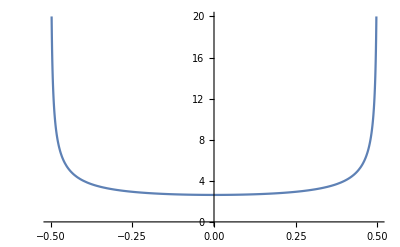

```mathematica
Plot[r/.(RTsameT/.{L->1,T->1})//Evaluate,{x,-1,1},PlotRange->{0,20}]
```

```mathematica
sameTuTv
```

{Tu→T,Tv→T}

```mathematica
RTsameT
```

r→(2 T Cosh[L T])/(√(Cosh[L T]^2-Cosh[2 T x]^2))

```mathematica
$Assumptions
```

u∈ℝ&&r∈ℝ&&v∈ℝ&&r>Tu+Tv>0&&Tu>0&&Tv>0&&L>0&&T>0&&r>2 T&&x∈ℝ

```mathematica
2π δq[ξ,δ@metric]/.sameTuTv/.{δTu->δT,δTv->δT}/.{u->x,v->x}//Simplify

%/.RTsameT//FullSimplify
```

(π (-1-ⅇ^(2 L T)+(ⅇ^(T (L-2 x)) r)/(√(r^2-4 T^2))+(ⅇ^(T (L+2 x)) r)/(√(r^2-4 T^2))) δT)/((-1+ⅇ^(2 L T)) G)

(π δT (-1+√(1/(Cosh[2 L T]-Cosh[4 T x])) √(Cosh[2 L T]-Cosh[4 T x])) Coth[L T])/G

0

#### Entropy in Poincare AdS without a cutoff

Note that the generators and the coefficients yields a ξ that has dimensions of length:

```mathematica
ju/@Range[-1,1]
```

{{1,0,0},{u,0,z/2},{u^2,-z^2,u z}}

```mathematica
coeffs
```

{(um up)/(-um+up),-(um+up)/(-um+up),1/(-um+up),(vm vp)/(-vm+vp),-(vm+vp)/(-vm+vp),1/(-vm+vp)}

```mathematica
ξR=Simplify[R ξ/.{u->x+t,v->x-t,up->xp,vp->xp,um->xm,vm->xm}/.{t->0,xp->√(d^2/4+zc^2),xm->-√(d^2/4+zc^2)}]
```

{(π R (d^2-4 (x^2+z^2-zc^2)))/(2 √(d^2+4 zc^2)),-(π R (d^2-4 (x^2+z^2-zc^2)))/(2 √(d^2+4 zc^2)),0}

```mathematica
ans=Simplify[δq[R ξ,δ@metric]/.{δTu->0,δTv->0,Tu->0,Tv->0},R>0]
```

1/(8 G (um-up) (vm-vp) z^2)R ((vm-vp) (u^2-z^2)+um (v^2-u vm+up vm+u vp-up vp+vm vp-v (vm+vp)-z^2)+up (-v^2-u vm+u vp-vm vp+v (vm+vp)+z^2)) δR

```mathematica
sans=Simplify[ans/.{u->x+t,v->x-t,up->xp,vp->xp,um->xm,vm->xm}/.{t->0,xp->√(d^2/4+zc^2),xm->-√(d^2/4+zc^2)}]
```

(R (d^2+4 (-x^2+z^2+zc^2)) δR)/(16 G z^2 √(d^2+4 zc^2))

```mathematica
tmp=Simplify[sans/.z->√(d^2/4-x^2+zc^2)]
```

(R δR)/(2 G √(d^2+4 zc^2))

```mathematica
Simplify[Integrate[tmp/.δR->1,d]]
```

(R (-Log[1-d/(√(d^2+4 zc^2))]+Log[1+d/(√(d^2+4 zc^2))]))/(4 G)